```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
trnM = Transpose@Import["./data/results/maynard/train_loss.csv"];
tstM = Transpose@Import["./data/results/maynard/test_loss.csv"];
trnC = Transpose@Import["./data/results/cnode/train_loss.csv"];
tstC = Transpose@Import["./data/results/cnode/test_loss.csv"];
```

```mathematica
ticks = Range[0.1,0.4,0.05];
```

```mathematica
StandardError[x_]:= StandardDeviation[x]/(√Length[x])
```

```mathematica
ErrorLogPlot[d1_,d2_,t_]:=Module[{data,error,max,min,pts,data2,error2,max2,min2,pts2},
	data = Mean@d1;
	error = StandardError@d1;
	max = data + error;
	min = data - error;
	pts = Thread[{ticks,data}];
	max = Thread[{ticks,max}];
	min = Thread[{ticks,min}];
	data2 = Mean@d2;
	error2 = StandardError@d2;
	max2 = data2 + error2;
	min2 = data2 - error2;
	pts2 = Thread[{ticks,data2}];
	max2 = Thread[{ticks,max2}];
	min2 = Thread[{ticks,min2}];
	Show[
		ListLogLogPlot[{min,max,min2,max2},Joined->True,
					Filling->{1 -> {2},3-> {4}},
					FillingStyle->Directive@{LightGray,Opacity[0.5]},
					Frame->True,
					FrameTicks->{{All,None},{All,None}}, 
					FrameTicksStyle->16,
					FrameLabel->{"σ","prediction error"},
					PlotRange->Full,
					PlotStyle->Directive@{Dashed,LightGray}
					],
		ListLogLogPlot[{pts,pts2},Joined->True,Frame->True,PlotLegends->{"Maynard","cNODE"}],
		ListLogLogPlot[{pts,pts2},PlotStyle->Directive[Thick, PointSize->0.03],Frame->True],
		ListLogLogPlot[{pts,pts2},PlotStyle->Directive[Thick, White, PointSize->0.015],Frame->True],
		PlotLabel->t,ImageSize->Large
		]
]
```

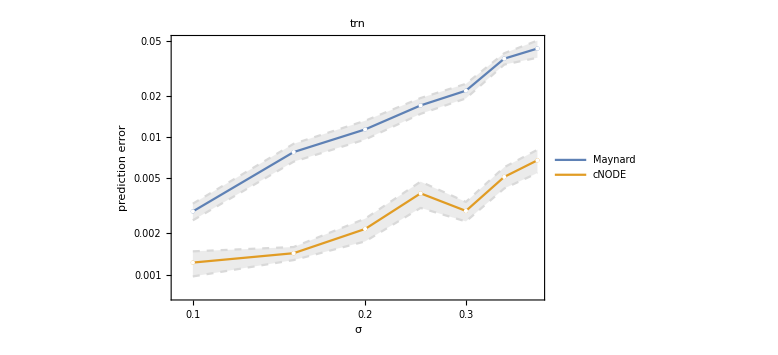

```mathematica
ErrorLogPlot[trnM,trnC,"trn"]
```

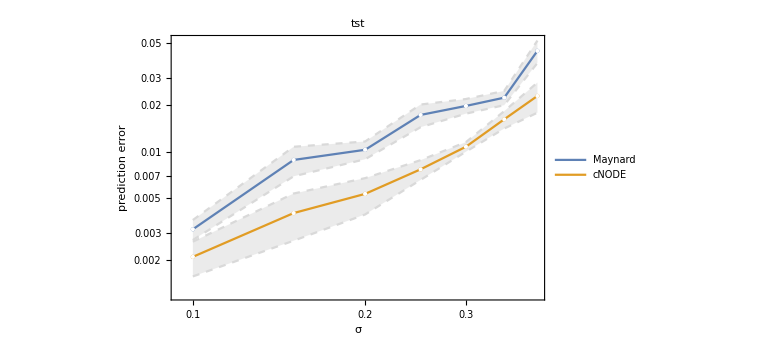

```mathematica
ErrorLogPlot[tstM,tstC,"tst"]
```